# Notebook For: Gravitational Radiation From Point Masses In A Keplerian Orbit by Peters and Mathews PRD July 1963

Geoff Cope
University of Utah
September 21st, 2021

## Hyperlink To Paper

```mathematica
Hyperlink["Gravitational Radiation From Point Masses In A Keplerian Orbit by Peters and Mathews PRD July 1963",
"https://journals.aps.org/pr/abstract/10.1103/PhysRev.131.435"]
```

[Gravitational Radiation From Point Masses In A Keplerian Orbit by Peters and Mathews PRD July 1963](https://journals.aps.org/pr/abstract/10.1103/PhysRev.131.435)

```mathematica
Hyperlink["Gravitational Radiation From Point Masses In A Keplerian Orbit by Peters and Mathews PRD July 1963",
"http://gravity.psu.edu/numrel/jclub/jc/Peters_Mathews_PR_131_435_1963.pdf"]
```

[Gravitational Radiation From Point Masses In A Keplerian Orbit by Peters and Mathews PRD July 1963](http://gravity.psu.edu/numrel/jclub/jc/Peters_Mathews_PR_131_435_1963.pdf)

## Utilities

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 2260 Kb

{Utilities`CleanSlate`,GeneralRelativityTensors`,Parallel`Debug`Perfmon`,Parallel`Debug`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,xAct`xPand`,xAct`xPert`,xAct`ExpressionManipulation`,xAct`xTensor`,xAct`xPerm`,xAct`xCore`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
Clear[eq11] (* Not numbered in paper *) 
eq11 = { 
d1[t] == (m2/(m1+m2))d[t] , 
d2[t] == (m1/(m1+m2)) d [t], 
μ == (m1 m2)/(m1+m2)
} ;
eq11 // TableForm
```

d1[t]==(m2 d[t])/(m1+m2)
d2[t]==(m1 d[t])/(m1+m2)
μ==(m1 m2)/(m1+m2)

```mathematica
eq11[[1;;2]] /. Equal-> Rule  // TableForm
```

d1[t]→(m2 d[t])/(m1+m2)
d2[t]→(m1 d[t])/(m1+m2)

```mathematica
eq11[[3]] /. Equal-> Rule
```

μ→(m1 m2)/(m1+m2)

```mathematica
Flatten[Solve[ eq11[[3]] , m1 ]] 
Flatten[Solve[ eq11[[3]] , m2 ]]
```

{m1→(m2 μ)/(m2-μ)}

{m2→(m1 μ)/(m1-μ)}

```mathematica
Clear[r1]
r1 = { d1[t] Cos[ψ[t]] , d1[t] Sin[ψ[t]] }
```

{Cos[ψ[t]] d1[t],d1[t] Sin[ψ[t]]}

```mathematica
Clear[r2]
r2 = {-  d2[t] Cos[ψ[t]] , - d2[t] Sin[ψ[t]] }
```

{-Cos[ψ[t]] d2[t],-d2[t] Sin[ψ[t]]}

```mathematica
Clear[r]
r = { r1 , r2 }
```

{{Cos[ψ[t]] d1[t],d1[t] Sin[ψ[t]]},{-Cos[ψ[t]] d2[t],-d2[t] Sin[ψ[t]]}}

```mathematica
Clear[m]
m = { m1 , m2 }
```

{m1,m2}

```mathematica
Clear[𝒬]
𝒬 = 
Table[ Sum[ m[[α]] r[[α]][[i]] r[[α]][[j]]  , {α,1,2} ]  , {i,1,2} , {j,1,2} ]   /.(  eq11[[1;;2]] /. Equal-> Rule )    // Expand // Simplify  ;
𝒬// MatrixForm
```

((m1 m2 Cos[ψ[t]]^2 d[t]^2)/(m1+m2) | (m1 m2 Cos[ψ[t]] d[t]^2 Sin[ψ[t]])/(m1+m2)
(m1 m2 Cos[ψ[t]] d[t]^2 Sin[ψ[t]])/(m1+m2) | (m1 m2 d[t]^2 Sin[ψ[t]]^2)/(m1+m2))

```mathematica
Clear[Q]
Q = 
𝒬 /. Flatten[Solve[ eq11[[3]] , m1 ]]   // Expand // Simplify   ;
Q // MatrixForm
```

(μ Cos[ψ[t]]^2 d[t]^2 | μ Cos[ψ[t]] d[t]^2 Sin[ψ[t]]
μ Cos[ψ[t]] d[t]^2 Sin[ψ[t]] | μ d[t]^2 Sin[ψ[t]]^2)

```mathematica
Clear[eq12]
eq12 = 
d[t] == (a(1-ℯ^2))/(1+ ℯ Cos[ψ])/. ψ-> ψ[t]  ;
eq12 /. Equal-> Rule
```

d[t]→(a (1-ℯ^2))/(1+ℯ Cos[ψ[t]])

```mathematica
Clear[eq13]
eq13 = 
ψ'[t] ==(√(G(m1 + m2 ) a (1-ℯ^2)))/d[t]^2 ;
eq13 /. Equal-> Rule
```

ψ'[t]→(√(a G (m1+m2) (1-ℯ^2)))/d[t]^2

```mathematica
Clear[psiPrime]
psiPrime = 
eq13 /. Equal-> Rule  //. (eq12 /. Equal-> Rule )  // Expand // Simplify
```

ψ'[t]→(√(-a G (m1+m2) (-1+ℯ^2)) (1+ℯ Cos[ψ[t]])^2)/(a^2 (-1+ℯ^2)^2)

```mathematica
Clear[psiDoublePrime]
psiDoublePrime = 
D[ psiPrime  , t ]  /. psiPrime
```

ψ''[t]→(2 G (m1+m2) ℯ (1+ℯ Cos[ψ[t]])^3 Sin[ψ[t]])/(a^3 (-1+ℯ^2)^3)

```mathematica
Clear[psiTriplePrime]
psiTriplePrime = 
D[ psiDoublePrime , t ]  /. psiPrime // Expand // Simplify
```

ψ^(3)[t]→-(2 ℯ (-a G (m1+m2) (-1+ℯ^2))^(3/2) (1+ℯ Cos[ψ[t]])^4 (Cos[ψ[t]]+ℯ (-1+2 Cos[2 ψ[t]])))/(a^6 (-1+ℯ^2)^6)

```mathematica
Clear[dPrime]
dPrime = 
D[ eq12 , t]  /. psiPrime /. Equal-> Rule
```

d'[t]→(ℯ (1-ℯ^2) √(-a G (m1+m2) (-1+ℯ^2)) Sin[ψ[t]])/(a (-1+ℯ^2)^2)

```mathematica
Clear[dDoublePrime]
dDoublePrime = 
D[ dPrime ,t ]  /. psiPrime // Expand  // Simplify
```

d''[t]→(G (m1+m2) ℯ Cos[ψ[t]] (1+ℯ Cos[ψ[t]])^2)/(a^2 (-1+ℯ^2)^2)

```mathematica
Clear[dTriplePrime]
dTriplePrime = 
D[ dDoublePrime , t ]  /. psiPrime // Expand // Simplify
```

d^(3)[t]→(ℯ (-a G (m1+m2) (-1+ℯ^2))^(3/2) (1+ℯ Cos[ψ[t]])^3 (1+3 ℯ Cos[ψ[t]]) Sin[ψ[t]])/(a^5 (-1+ℯ^2)^5)

```mathematica
Clear[dPsiDerivatives]
dPsiDerivatives = { 
psiPrime , 
psiDoublePrime , 
psiTriplePrime , 
dPrime  , 
dDoublePrime , 
dTriplePrime 
} ;
dPsiDerivatives  // TableForm
```

ψ'[t]→(√(-a G (m1+m2) (-1+ℯ^2)) (1+ℯ Cos[ψ[t]])^2)/(a^2 (-1+ℯ^2)^2)
ψ''[t]→(2 G (m1+m2) ℯ (1+ℯ Cos[ψ[t]])^3 Sin[ψ[t]])/(a^3 (-1+ℯ^2)^3)
ψ^(3)[t]→-(2 ℯ (-a G (m1+m2) (-1+ℯ^2))^(3/2) (1+ℯ Cos[ψ[t]])^4 (Cos[ψ[t]]+ℯ (-1+2 Cos[2 ψ[t]])))/(a^6 (-1+ℯ^2)^6)
d'[t]→(ℯ (1-ℯ^2) √(-a G (m1+m2) (-1+ℯ^2)) Sin[ψ[t]])/(a (-1+ℯ^2)^2)
d''[t]→(G (m1+m2) ℯ Cos[ψ[t]] (1+ℯ Cos[ψ[t]])^2)/(a^2 (-1+ℯ^2)^2)
d^(3)[t]→(ℯ (-a G (m1+m2) (-1+ℯ^2))^(3/2) (1+ℯ Cos[ψ[t]])^3 (1+3 ℯ Cos[ψ[t]]) Sin[ψ[t]])/(a^5 (-1+ℯ^2)^5)

```mathematica
Q[[1,1]]  /. (  eq11[[3]] /. Equal-> Rule  )/. ( eq12 /. Equal-> Rule   )
```

(a^2 m1 m2 (1-ℯ^2)^2 Cos[ψ[t]]^2)/((m1+m2) (1+ℯ Cos[ψ[t]])^2)

```mathematica
Clear[eq14a]
eq14a = 
D[ Q[[1,1]] , {t,3} ]  /. (  eq11[[3]] /. Equal-> Rule  )/. ( eq12 /. Equal-> Rule   )   /. dPsiDerivatives // Expand // Simplify
```

-(G m1 m2 √(-a G (m1+m2) (-1+ℯ^2)) (1+ℯ Cos[ψ[t]])^2 (4+3 ℯ Cos[ψ[t]]) Sin[2 ψ[t]])/(a^3 (-1+ℯ^2)^3)

```mathematica
Clear[eq14b]
eq14b = 
D[ Q[[1,2]] , {t,3} ]   /. (  eq11[[3]] /. Equal-> Rule  )/. ( eq12 /. Equal-> Rule   )   /. dPsiDerivatives // Expand // Simplify
```

(G m1 m2 √(-a G (m1+m2) (-1+ℯ^2)) (1+ℯ Cos[ψ[t]])^2 (5 ℯ Cos[ψ[t]]+8 Cos[2 ψ[t]]+3 ℯ Cos[3 ψ[t]]))/(2 a^3 (-1+ℯ^2)^3)

```mathematica
Clear[eq14c]
eq14c = 
D[ Q[[2,2]] , {t,3} ]   /. (  eq11[[3]] /. Equal-> Rule  )/. ( eq12 /. Equal-> Rule   )   /. dPsiDerivatives // Expand // Simplify
```

(G m1 m2 √(-a G (m1+m2) (-1+ℯ^2)) (1+ℯ Cos[ψ[t]])^2 (8 Cos[ψ[t]]+ℯ (5+3 Cos[2 ψ[t]])) Sin[ψ[t]])/(a^3 (-1+ℯ^2)^3)

```mathematica
PowerExpand[ eq14c , Assumptions -> ℯ > 0  && ℯ < 1 && a > 0  && G > 0  && m1 > 0 && m2 > 0  ]    // PowerExpand
```

(8 G^(3/2) m1 m2 √(m1+m2) √(1-ℯ^2) Cos[ψ[t]] (1+ℯ Cos[ψ[t]])^2 Sin[ψ[t]])/(a^(5/2) (-1+ℯ^2)^3)+(G^(3/2) m1 m2 √(m1+m2) ℯ √(1-ℯ^2) (1+ℯ Cos[ψ[t]])^2 (5+3 Cos[2 ψ[t]]) Sin[ψ[t]])/(a^(5/2) (-1+ℯ^2)^3)

```mathematica
Clear[eq14d]
eq14d = 
β^2== (4 G^3 m1^2 m2^2(m1+m2))/(a^5 (1-ℯ^2)^5)
```

β^2==(4 G^3 m1^2 m2^2 (m1+m2))/(a^5 (1-ℯ^2)^5)

```mathematica
ApplySides[ Sqrt , eq14d ]  // PowerExpand
```

β==(2 G^(3/2) m1 m2 √(m1+m2))/(a^(5/2) (1-ℯ^2)^(5/2))

```mathematica
PowerExpand[Sqrt[x y],Assumptions->Pi/2<Arg[x]<Pi&&Pi/2<Arg[y]<Pi]
```

-√x √y

```mathematica
Clear[qThirdD]
qThirdD= 
D[𝒬 , {t,3} ] /. (  eq11[[3]] /. Equal-> Rule  )/. ( eq12 /. Equal-> Rule   )   /. dPsiDerivatives // Expand // Simplify  ;
qThirdD  // MatrixForm
```

(-(G m1 m2 √(-a G (m1+m2) (-1+ℯ^2)) (1+ℯ Cos[ψ[t]])^2 (4+3 ℯ Cos[ψ[t]]) Sin[2 ψ[t]])/(a^3 (-1+ℯ^2)^3) | (G m1 m2 √(-a G (m1+m2) (-1+ℯ^2)) (1+ℯ Cos[ψ[t]])^2 (5 ℯ Cos[ψ[t]]+8 Cos[2 ψ[t]]+3 ℯ Cos[3 ψ[t]]))/(2 a^3 (-1+ℯ^2)^3)
(G m1 m2 √(-a G (m1+m2) (-1+ℯ^2)) (1+ℯ Cos[ψ[t]])^2 (5 ℯ Cos[ψ[t]]+8 Cos[2 ψ[t]]+3 ℯ Cos[3 ψ[t]]))/(2 a^3 (-1+ℯ^2)^3) | (G m1 m2 √(-a G (m1+m2) (-1+ℯ^2)) (1+ℯ Cos[ψ[t]])^2 (8 Cos[ψ[t]]+ℯ (5+3 Cos[2 ψ[t]])) Sin[ψ[t]])/(a^3 (-1+ℯ^2)^3))

```mathematica
Clear[eq15a] (* problem is trying to check the trig functions - they do check.... this is a correct expression  *) 
eq15a = 
(G/(5 c^5)) *  Sum[ qThirdD[[i,j]] qThirdD[[i,j]] -(1/3) qThirdD[[i,i]]qThirdD[[j,j]] , {i,1,2} , {j,1,2} ]  // Expand  // Simplify
```

-(4 m1^2 m2^2 (m1+m2) (G+G ℯ Cos[ψ[t]])^4 (24+13 ℯ^2+48 ℯ Cos[ψ[t]]+11 ℯ^2 Cos[2 ψ[t]]))/(15 a^5 c^5 (-1+ℯ^2)^5)

```mathematica
eq15a  //. ψ[t]-> ψ
```

-(4 m1^2 m2^2 (m1+m2) (G+G ℯ Cos[ψ])^4 (24+13 ℯ^2+48 ℯ Cos[ψ]+11 ℯ^2 Cos[2 ψ]))/(15 a^5 c^5 (-1+ℯ^2)^5)

```mathematica
(* SEE LAST SUM IN THE APPENDIX *) 
(* no idea why these are wrong.... 192/30 is 32/5 other fractions are off and power in denomiator should be 7/2  *) 
(* How to do this properly is explained on page 259 of General Relativity by Straumann... see how to do the averaging *) 
(* Factor in front should be one over the period *) 
Clear[eq16]
eq16 = 
(1/π)*Integrate[ ( eq15a  //. ψ[t]-> ψ  ) , {ψ,0,π } ]
```

-(G^4 m1^2 m2^2 (m1+m2) (192+1448 ℯ^2+1092 ℯ^4+61 ℯ^6))/(30 a^5 c^5 (-1+ℯ^2)^5)

```mathematica
Clear[eq17]
eq17 = 
f[ℯ] == (1 + (73/24)ℯ^2+ (37/96) ℯ^4)/((1-ℯ^2)^(7/2))
```

f[ℯ]==(1+(73 ℯ^2)/24+(37 ℯ^4)/96)/((1-ℯ^2)^(7/2))

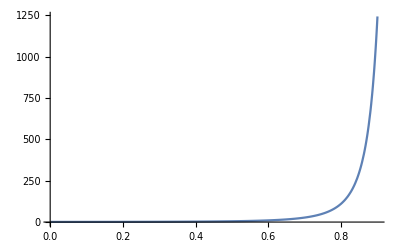

```mathematica
Plot[ eq17[[2]] , {ℯ,0.001 , 0.9 } , PlotRange-> All  ]
```

```mathematica
eq17[[2]] /. ℯ-> 0.6 
eq17[[2]] /. ℯ-> 0.8 
eq17[[2]] /. ℯ-> 0.9
```

10.2279

110.902

1243.11